```mathematica
Boole[PrimeQ[ChineseRemainder[#,{5,7,11,13,17}]]]&/@Tuples[{1,2},5]
```

{0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,1,0,1,0,0,0,1}

```mathematica
Reduce[{Mod[x,7]==3,Mod[x,5]==2,Mod[x,3]==1},x,Integers]
```

C[1]∈Integers&&x==52+105 C[1]

```mathematica
ChineseRemainder[{3,2,1},{7,5,3}]
```

52

```mathematica
{x}~Join~#~Join~{a}&/@Tuples[{2,3},3]
```

{{x,2,2,2,a},{x,2,2,3,a},{x,2,3,2,a},{x,2,3,3,a},{x,3,2,2,a},{x,3,2,3,a},{x,3,3,2,a},{x,3,3,3,a}}

```mathematica
{1,{1,2},{1,2,3}}
```

```mathematica
Tuples[{{1,2,3},{a,b},{5,6}}]
```

{{1,a,5},{1,a,6},{1,b,5},{1,b,6},{2,a,5},{2,a,6},{2,b,5},{2,b,6},{3,a,5},{3,a,6},{3,b,5},{3,b,6}}

```mathematica
b={{n___,d,x_,m___}:> {n,x,d,m},{n_,m___,d}->{n,d,m}}
```

{{n___,d,x_,m___}:>{n,x,d,m},{n_,m___,d}→{n,d,m}}

```mathematica
Nest[ReplaceAll,b,4]
```

```mathematica
Nest[ReplaceAll[#,b]&,{d,0,0,1,n,0,0,1},8]
```

{0,d,0,1,n,0,0,1}

```mathematica
f[{x___,d_,n___},d_:>{a_,y__}]:=Join[{{x,a,n}},f[{x,d,n},d->{y}]]
```

```mathematica
f[{x___,d_,n___},d_->{a_}]:={{x,a,n}}
f[{1,2,3,5},1->{q,w,e,r,t,y,u}]
```

{{q,2,3,5},{w,2,3,5},{e,2,3,5},{r,2,3,5},{t,2,3,5},{y,2,3,5},{u,2,3,5}}

```mathematica
d[{a___},g:(x_->{b__}),y__]:={f[{a},g],d[{a},y]}
```

```mathematica
d[{1,2,3,4},1->{q,2},2->{r,u}]
```

```mathematica
{{{q,2,3,4},{2,2,3,4}},{{1,r,3,4},{1,u,3,4}}}
```

```mathematica
Table[(Table[Fibonacci[n]//PrimeQ//Boole,{n,1,m}]/.  0->Sequence[])//Length,{m,1,1000}]//Split//Map[Length,#]&
```

{2,1,1,2,4,2,4,6,6,14,4,36,48,6,222,72,2,16,60,60,2,430}

```mathematica
{2,1,1,2,4,2,4,6,6,14,4,36,48,6,222,72,2,16,60,60,2}
```

{2,1,1,2,4,2,4,6,6,14,4,36,48,6,222,72,2,16,60,60,2}

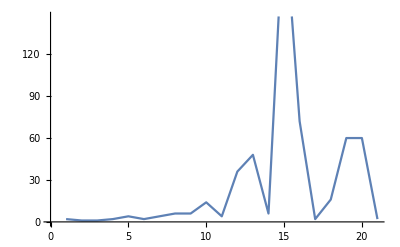

```mathematica
ListLinePlot[{2,1,1,2,4,2,4,6,6,14,4,36,48,6,222,72,2,16,60,60,2}]
```

```mathematica
g[x_]:=If[PrimeQ[x]&&(PrimeQ[x+2]||PrimeQ[x-2]),1,0]
```

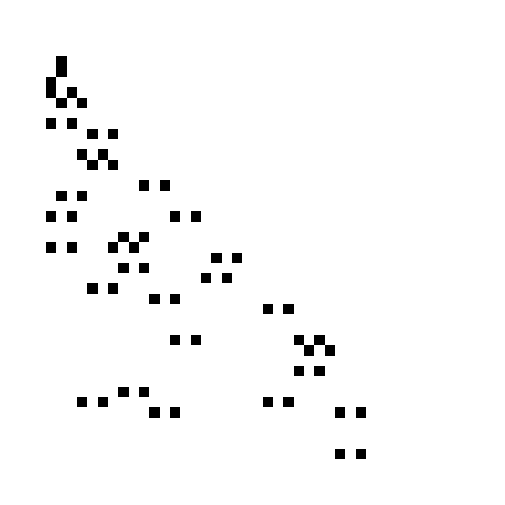

```mathematica
a=1;Table[g[a++],{m,1,40},{n,1,m}]//ArrayPlot
```

```mathematica
h[x_]:=Flatten[Rest[Rest[IntegerPartitions[#,2]]&/@Range[x]],1]
```

```mathematica
h[5]
```

{{1,1},{2,1},{3,1},{2,2},{4,1},{3,2}}

```mathematica
Part[Table[Mod[n,m],{n,1,10},{m,1,n}],#1,#2]&@@@f[10]
```

{0,0,0,0,0,1,0,0,0,0,1,1,0,0,2,0,0,1,0,1,0,0,1,2,0}

```mathematica
ff[{y__},x_]:=Part[{y},Sequence @@(Rest[IntegerPartitions[x,2]])]
```

```mathematica
f1[x_]:=Rest[Rest[IntegerPartitions[#,2]]&/@Range[x]]
```

```mathematica
h[x_]:=Flatten[Rest[Rest[IntegerPartitions[#,2]]&/@Range[x]],1]
```

```mathematica
f1[10]//Column
```

{{1,1}}
{{2,1}}
{{3,1},{2,2}}
{{4,1},{3,2}}
{{5,1},{4,2},{3,3}}
{{6,1},{5,2},{4,3}}
{{7,1},{6,2},{5,3},{4,4}}
{{8,1},{7,2},{6,3},{5,4}}
{{9,1},{8,2},{7,3},{6,4},{5,5}}

```mathematica
Table[Mod[n,m],{n,1,10},{m,1,n}][[#1,#2]]&@@@ff[10]
```

{0,0,1,2,0}

```mathematica
{{{0}}, {{0,0}}, {{0,1,0}}, {{0,0,1,0}}, {{0,1,2,1,0}}, {{0,0,0,2,1,0}}, {{0,1,1,3,2,1,0}}, {{0,0,2,0,3,2,1,0}}, {{0,1,0,1,4,3,2,1,0}}, {{0,0,1,2,0,4,3,2,1,0}}}//ff[#,10]&
```

```mathematica
ff[9]
```

{{8,1},{7,2},{6,3},{5,4}}

```mathematica
Total/@(d[100,#]&/@Range[100])
```

{0,0,0,0,1,0,2,1,2,2,4,1,5,4,4,4,7,4,8,5,7,8,10,5,10,10,10,9,13,8,14,11,13,14,14,10,17,16,16,13,19,14,20,17,17,20,22,15,22,20,22,21,25,20,24,21,25,26,28,19,29,28,26,26,29,26,32,29,31,28,34,25,35,34,32,33,35,32,38,31,36,38,40,31,39,40,40,37,43,34,42,41,43,44,44,37,47,44,44,42}

```mathematica
FindSequenceFunction[%115,n]
```

{0,0,0,0,1,0,2,1,2,2,4,1,5,4,4,4,7,4,8,5,7,8,10,5,10,10,10,9,13,8,14,11,13,14,14,10,17,16,16,13,19,14,20,17,17,20,22,15,22,20,22,21,25,20,24,21,25,26,28,19,29,28,26,26,29,26,32,29,31,28,34,25,35,34,32,33,35,32,38,31,36,38,40,31,39,40,40,37,43,34,42,41,43,44,44,37,47,44,44,42}

```mathematica
d[a1_,a_]:=Apply[Table[Mod[n,m],{n,1,a1},{m,1,n}]⟦#1,#2⟧&,ff[a],{1}]
```

```mathematica
Table[d[n,n],{n,1,20}]//Column
```

{}
{0}
{0}
{0,0}
{0,1}
{0,0,0}
{0,1,1}
{0,0,2,0}
{0,1,0,1}
{0,0,1,2,0}
{0,1,2,3,1}
{0,0,0,0,2,0}
{0,1,1,1,3,1}
{0,0,2,2,4,2,0}
{0,1,0,3,0,3,1}
{0,0,1,0,1,4,2,0}
{0,1,2,1,2,5,3,1}
{0,0,0,2,3,0,4,2,0}
{0,1,1,3,4,1,5,3,1}
{0,0,2,0,0,2,6,4,2,0}